```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/BV12Q.csv"]; 
userconfig=<|
NQubits-> 13,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,12],{{1,1,0},{3,2,0},{3,0,0},{4,2,0},{4,0,0},{5,2,0},{5,0,0},{0,2,0},{0,0,0},{1,2,0},{1,0,0},{2,2,0},{2,0,0}}}](*,{1,2,0}}}]*),
(* blockade radius in μm*)
BlockadeRadius->10,
(*BlockadeRadius->3,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 98,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[Gates][[All,1]]
RydDev[InitLocations]

data[[5]];
d=data[[5]][[3;;data[[2,1]]+2]];
Length[data]
Fraction[a_,b_]:=a/b
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations]
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAPDCG_(q1$_Integer,q2$_Integer),SWAPDCH_(q1$_Integer,q2$_Integer),InstaSWAP_(q1_,q2_),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$6311,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$6311[{p$,q$}],CZG_(p$_Integer,q$_Integer)/;blockadeCheck$6311[{p$,q$}],CZH_(p$_Integer,q$_Integer)/;blockadeCheck$6311[{p$,q$}],CCZ_(i$_,j$_,k$_)/;blockadeCheck$6311[{i$,j$}]/;blockadeCheck$6311[{j$,k$}]/;blockadeCheck$6311[{k$,i$}],C_c$_[Z_t$__]/;blockadeCheck$6311[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$6311[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$6311[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

-Graphics3D-

8188

<|0→{1,1,0},1→{3,2,0},2→{3,0,0},3→{4,2,0},4→{4,0,0},5→{5,2,0},6→{5,0,0},7→{0,2,0},8→{0,0,0},9→{1,2,0},10→{1,0,0},11→{2,2,0},12→{2,0,0}|>

```mathematica
Total[Table[2^i,{i,2,12}]]
```

8188

```mathematica
InsertCircuitNoise[{Subscript[ShiftLoc, 0][{3,0,0}]},RydDev];
RydDev[QubitLocations]
RydDev[PlotAvailQubits][]
Reg=CreateDensityQureg[2];
InitClassicalState[Reg,3];
ApplyCircuit[Reg,ExtractCircuit[GetCircuitSchedule[{Subscript[CZ, 1,0][Pi]},RydDev,ReplaceAliases->True]]]
CalcProbOfAllOutcomes[Reg,{0,1}]
?ShiftLoc
```

<|0→{1,1,0},1→{3,2,0},2→{3,0,0},3→{4,2,0},4→{4,0,0},5→{5,2,0},6→{5,0,0},7→{0,2,0},8→{0,0,0},9→{1,2,0},10→{1,0,0},11→{2,2,0},12→{2,0,0}|>

-Graphics3D-

{}

{0.,0.,0.,1.}

16

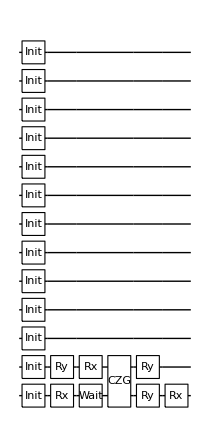
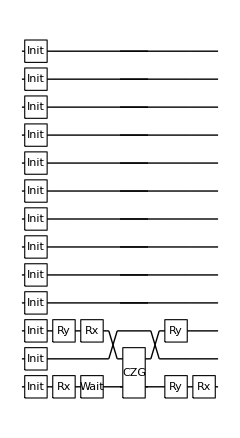
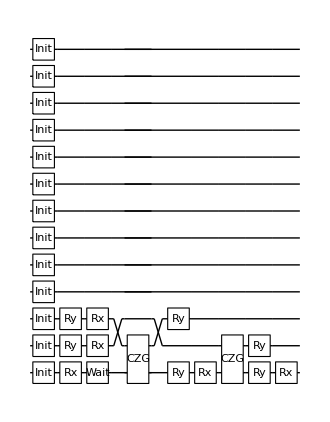
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CircuitTranslator[DataSet_]:=Table[CircSplit=DataSet[[i,3;;DataSet[[i,1]]+2]];CZCount=0;
(*Print[CircSplit];*)ZonesMoved=0;
TransCirc=Join[Table[Subscript[Init, j],{j,0,userconfig[NQubits]-1}],Flatten[Table[GateSplit=StringSplit[CircSplit[[j]],", ["];
GateName=StringTrim[StringTrim[GateSplit[[1]],"["],"'"];
GateQubits=IntegerPart[ToExpression[StringSplit[StringTrim[GateSplit[[2]],"]"],","]]];
GateParameters=If[StringContainsQ[GateName,"C"],Pi,Pi*ToExpression[StringReplace[StringTrim[GateSplit[[3]],"]]"],{"("->"[",")"->"]"}]]];
If[Length[GateQubits]==2,CZCount+=1;If[GateQubits[[1]]<=(userconfig[NQubits]-1)-6*(ZonesMoved+1),MoveSize=((userconfig[NQubits]-1)-Ceiling[GateQubits[[1]],6])/2;ZonesMoved+=MoveSize/3;{Subscript[Wait, 0][40],Subscript[CZG,GateQubits[[1]],GateQubits[[2]]]},Subscript[CZG,GateQubits[[1]],GateQubits[[2]]]],Subscript[ToExpression[GateName], GateQubits[[1]]][GateParameters]],{j,1,DataSet[[i,1]]}]]];
(*Print["Circuit number",i,"CZCount",CZCount];*)TransCirc
,{i,1,Length[DataSet]}]
(*a=data[[2;;Length[data]]][[1]][[3;;9]]*)
Circs=CircuitTranslator[data];
Table[(*ExtractCircuit[InsertCircuitNoise[*)DrawCircuit[Circs[[i]]](*,RydDev,ReplaceAliases->True]]*),{i,1,4}]
```

```mathematica
{Subscript[Init, q$_Integer],Subscript[Wait, qubits$__][dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},Subscript[M, q$_Integer],Subscript[SRot, q$_Integer][ϕ$_,Δ$_,tg$_],Subscript[H, q$_Integer],Subscript[Rx, q$_Integer][θ$_],Subscript[Ry, q$_Integer][θ$_],Subscript[Rz, q$_Integer][θ$_],Subscript[SWAP, q1$_Integer,q2$_Integer],Subscript[SWAPLoc, q1$_Integer,q2$_Integer],Subscript[ShiftLoc, q$__][v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1852814,v$],Subscript[CZ, p$_Integer,q$_Integer][ϕ$_]/;blockadeCheck$1852814[{p$,q$}],Subscript[C, c$_][Subscript[Z, t$__]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$_][Subscript[Z, t$__][θ$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_][θ$_]]}
```

```mathematica
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
KetList[2]
Length[%]
RydDev[PlotAvailQubits][]
```

{{0,0},{0,1},{1,0},{1,1}}

4

-Graphics3D-

```mathematica
{"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

16

```mathematica
percent2infidel[num_]:=Module[{},Assert[0<=num<=100,"number is in percent"];1-0.01 num];
Circs=CircuitTranslator[data];
```

```mathematica
(*BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[InitZeroState[ρ];ApplyCircuit[ρ,Join[ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,Nq-1}],Circs[[i]]],RydDev,ReplaceAliases->True]],Flatten[Table[{Subscript[Depol, q][1-0.01*99.7] ,ExtractCircuit[InsertCircuitNoise[{Subscript[Wait, q][2*10^4]},RydDev,ReplaceAliases->True]]},{q,1,Nq-1}]]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]*)
BVCircuitApplier[Circs_,Nq_]:= Table[ρ=CreateDensityQureg[13];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Circs[[i]],RydDev,ReplaceAliases->True]]];
ProbsAllStates=CalcProbOfAllOutcomes[ρ,Range[1,12]];
RenormProbs=Total[CalcProbOfAllOutcomes[ρ,Range[0,12]]];
RenormProbsAllStates=ProbsAllStates/RenormProbs;
DestroyAllQuregs[];
{ProbsAllStates,RenormProbs,RenormProbsAllStates},
{i,1,Length[Circs]}]

i=Total[Table[2^NQ,{NQ,2,8}]]
RydDev[PlotAvailQubits][]
Table[Print[Nq];If[Nq>=10,LowestGateState=Total[Table[2^nqcount,{nqcount,2,Nq-2}]]+1;HighestGateState=Total[Table[2^nqcount,{nqcount,2,Nq-1}]];Data=BVCircuitApplier[Join[{Circs[[LowestGateState]]},RandomSample[Circs[[i+1;;i+2^(Nq-1)-2]],254],{Circs[[HighestGateState]]}],Nq],Data=BVCircuitApplier[Circs[[i;;i+2^(Nq-1)-1]],Nq]];
Probs={Mean[Max@@@Data[[All,1]]],StandardDeviation[Max@@@Data[[All,1]]]/Sqrt[Length[Max@@@Data[[All,1]]]]};
ProbsRenorm={Mean[Max@@@Data[[All,3]]],Abs[Mean[Max@@@Data[[All,3]]]]/Sqrt[Length[Max@@@Data[[All,3]]]]*Sqrt[(StandardDeviation[Max@@@Data[[All,1]]]/Mean[Max@@@Data[[All,1]]])^2+(StandardDeviation[Data[[All,2]]]/Mean[Data[[All,2]]])^2-2*Covariance[Max@@@Data[[All,1]],Data[[All,2]]]/(Mean[Max@@@Data[[All,1]]]*Mean[Data[[All,2]]])],StandardDeviation[Max@@@Data[[All,3]]]/Sqrt[Length[Max@@@Data[[All,3]]]]};PLoss={1-Mean[Data[[All,2]]],StandardDeviation[Data[[All,2]]]/Sqrt[Length[Data[[All,2]]]]};
i=i+2^(Nq-1);
Print[{Probs,ProbsRenorm,PLoss}];
{Probs,ProbsRenorm,PLoss},{Nq,10,13}]





(*If[Nq>9,LowestGateState=Total[Table[2^nqcount,{nqcount,2,Nq-1}]]+1;HighestGateState=Total[Table[2^nqcount,{nqcount,2,Nq}]];Data=BVCircuitApplier[Join[Circs[[LowestGateState]],RandomSample[Circs,254],Circs[[HighestGateState]]]],Data=BVCircuitApplier[Circs[[i;;i+2^(Nq-1)-1]],ρ,Nq]]*)
```

508

-Graphics3D-

10

{{0.901763,0.000228196},{0.998931,0.0000228081,0.0000228068},{0.0972732,0.000207834}}

11

{{0.900877,0.000232734},{0.998879,0.0000229118,0.0000229015},{0.0981136,0.000212729}}

12

{{0.899656,0.000253536},{0.998843,0.0000239822,0.0000239934},{0.0993029,0.000233701}}

13

{{0.898773,0.000244353},{0.998718,0.0000366519,0.0000366943},{0.100075,0.000221781}}

{{{0.901763,0.000228196},{0.998931,0.0000228081,0.0000228068},{0.0972732,0.000207834}},{{0.900877,0.000232734},{0.998879,0.0000229118,0.0000229015},{0.0981136,0.000212729}},{{0.899656,0.000253536},{0.998843,0.0000239822,0.0000239934},{0.0993029,0.000233701}},{{0.898773,0.000244353},{0.998718,0.0000366519,0.0000366943},{0.100075,0.000221781}}}

```mathematica
Max@@@{{0,1},{2,3}}
```

{1,3}

```mathematica
BVData2Dto12D={{{0.9103269038982479,0.0009788544692438548},{0.9997681923573765,0.00009488858838840734,0.0000948898351708522},{0.08946228061036965,0.0008926618228980903}},{{0.909129057143952,0.0007841750479236026},{0.9996513552049595,0.0000764870770446292,0.00007648895508904304},{0.09055425207572476,0.0007148636434052621}},{{0.9079322106226035,0.0006180492097694685},{0.9995338961291619,0.00006065470826908685,0.00006065688127008512},{0.09164491398338026,0.0005632159962750999}},{{0.9067363645366819,0.0004802636814320388},{0.999415815354451,0.000047421468060911236,0.00004742369486634815},{0.09273426790383665,0.00043749569319160393}},{{0.9055415190864888,0.00036873763456599784},{0.9992971131064503,0.00003663144131059494,0.000036633564174040825},{0.09382231540571029,0.00033577935402163907}},{{0.9043518326367831,0.0002801918696960662},{0.9991823874319673,0.000027914907548562137,0.000027917086487223874},{0.09490905805573702,0.0002551378023087078}},{{0.9031638473727539,0.00021111447185673233},{0.9990678291129284,0.00002106311349492649,0.00002106488952130282},{0.09599449741877297,0.0001922567365030836}},{{0.9017633922111741,0.00022819621627610066},{0.9989314158324039,0.000022808143360122204,0.000022806841576487807},{0.09727317645625821,0.00020783448802727254}},{{0.9008768657529446,0.00023273370850187652},{0.9988792947410556,0.000022911761275509944,0.000022901454806666252},{0.09811360000213498,0.00021272856936878156}},{{0.8996562009350657,0.0002535359465765697},{0.9988428881794796,0.000023982192613321724,0.000023993384562475887},{0.09930291381081391,0.0002337010554918799}},{{0.8987727472123339,0.0002443529997239817},{0.998718077842419,0.00003665194599531797,0.00003669433491077547},{0.10007497415232125,0.000221781173459564}}}
```